```mathematica
f[x_]:=E^((1/2)(1-x)) (* outer approximation *)
```

```mathematica
g[x_] :=E^(1/2)(E^(-x/2) - E^(-2x/err)) (* exact approx *)
```

```mathematica
h[x_] := E^(1/2) * (1-E^(-2*x/err)) (* inner approx *)
```

```mathematica
err=0.1
```

0.1

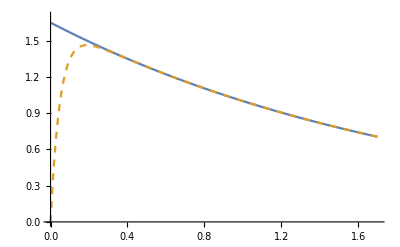

```mathematica
Plot[{f[x],g[x]}, {x, 0, 1.7},PlotRange -> {0,1.7},PlotStyle->{Dashing,Directive[Dashed],Directive[Thick]}]
```

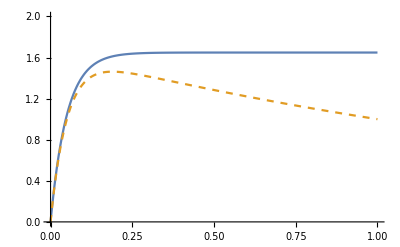

```mathematica
Plot[{h[x],g[x]}, {x, 0, 1},PlotRange -> {0,2},PlotStyle->{Dashing,Directive[Dashed],Directive[Thick]}]
```

```mathematica
a2[e_]:=1+Sqrt[1-e]
```

```mathematica
y[x_, e_]:=1/(E^(-a1[e]) - E^(-a2[e]/e)) * (e^(-a1[e]x) - e^((-a2[e]x)/e))
```

```mathematica
y[x,e]
```

(-e^(((-1-√(1-e)) x)/e)+e^(-((1-√(1-e)) x)/e))/(-ⅇ^((-1-√(1-e))/e)+ⅇ^(-(1-√(1-e))/e))